```mathematica
grad = {212,212,213,215,213,213,213}
```

{212,212,213,215,213,213,213}

```mathematica
minute = {42,42,5,22,58,53,44}
```

{42,42,5,22,58,53,44}

```mathematica
second = {37,19,28,52,30,30,55}
```

{37,19,28,52,30,30,55}

```mathematica
minute = minute/60
```

{7/10,7/10,1/12,11/30,29/30,53/60,11/15}

```mathematica
second = second/3600
```

{37/3600,19/3600,7/900,13/900,1/120,1/120,11/720}

```mathematica
data = grad+minute+second
```

{765757/3600,765739/3600,95891/450,193843/900,8559/40,25667/120,153899/720}

```mathematica
data = data - (160.0+11/60+57/3600)
```

{52.5111,52.5061,52.8919,55.1819,53.7758,53.6925,53.5494}

```mathematica
data = Sin[((data+62.0+57/60+37/3600)/2)/180*π]/Sin[((62.0+57/60+37/3600)/2)/180*π]
```

{1.61928,1.61924,1.62267,1.64267,1.63047,1.62974,1.62848}

```mathematica
data = data - 0.0
```

{1.61928,1.61924,1.62267,1.64267,1.63047,1.62974,1.62848}

```mathematica
plotdata = {{579,data⟦1⟧},{ 586,data⟦2⟧},{546.07,data⟦3⟧},{ 435,data⟦4⟧},{ 491.61,data⟦5⟧},{ 497.36,data⟦6⟧},{503,data⟦7⟧}}
```

{{579,1.61928},{586,1.61924},{546.07,1.62267},{435,1.64267},{491.61,1.63047},{497.36,1.62974},{503,1.62848}}

```mathematica
Export
```

```mathematica
line = NonlinearModelFit[plotdata,1+a/(b-4*π^2/λ^2),{a,b},λ]
```

FittedModel[1+0.00156998/(0.00265268-(4 π^2)/λ^2)]

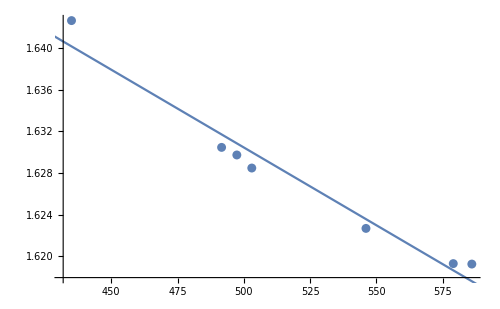

```mathematica
Show[
ListPlot[plotdata,ImageSize->500],
Plot[Normal@line,{x,0,600}]
]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

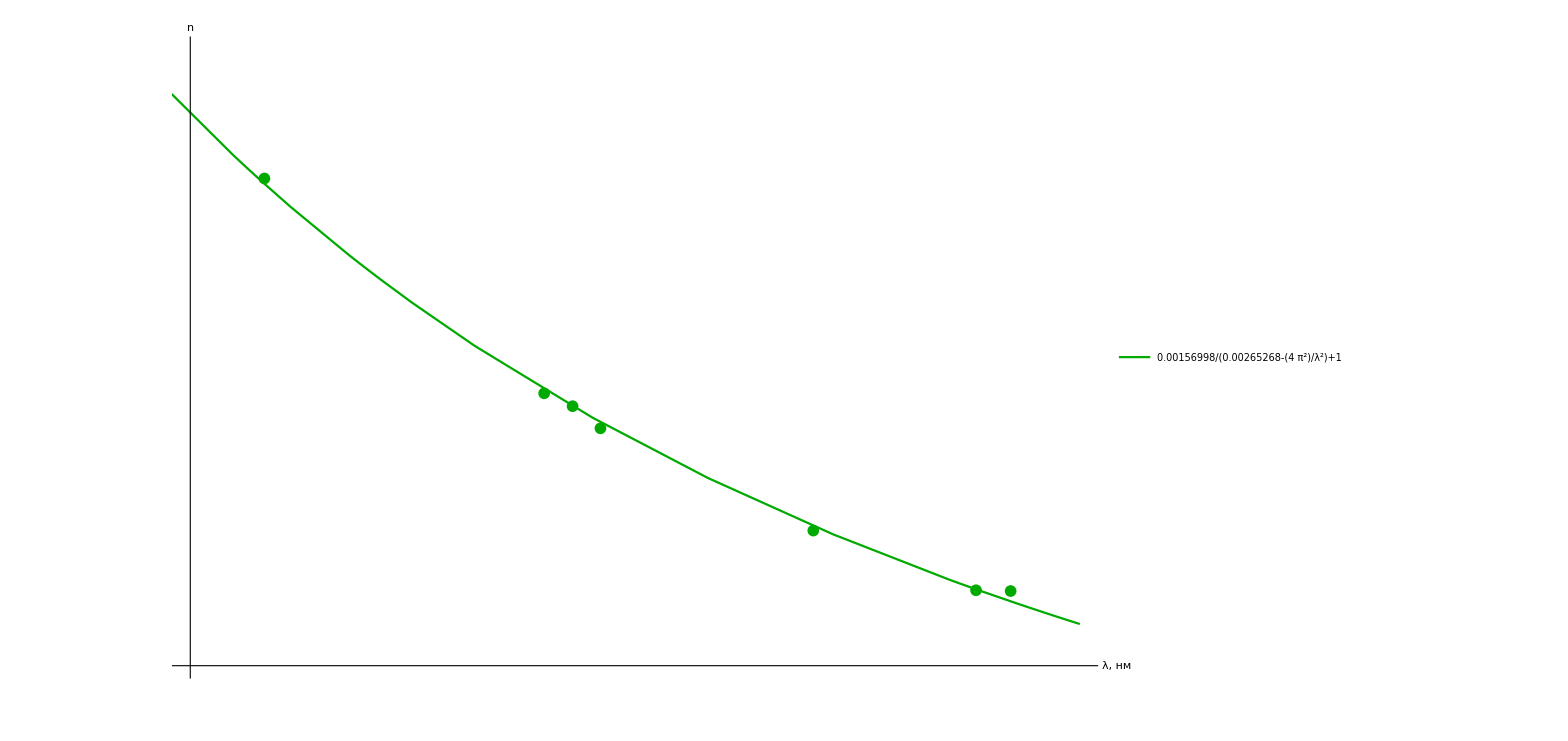

```mathematica
Show[
ListPlot[
plotdata,

PlotRange->{{420,600},{1.615,1.65}},

Ticks-> {Range[-700,700,10],Range[-100,1000,0.005]},

GridLines->{Range[-1000,1000,2], Range[-1000,1000,0.001]},

AxesLabel->{Style["λ, нм",Large],Style["n",Large]},

TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1200,
LabelStyle->Black,
PlotStyle->Darker@Green
],
Plot[
{Normal@line},
{λ,-600, 600},
PlotLegends->Placed[
LineLegend[ 
{Normal@line, line["ParameterTable"]},
LabelStyle->20,
LegendFunction->frame
],
{Scaled[0.7],Scaled[0.83]}
],
PlotStyle->Darker@Green
]
]
```

```mathematica
List
```

```mathematica
D[1+0.0015699769941772853/(0.002652684134341411-(4 π^2)/λ^2),λ]
```

-0.12396/((0.00265268-(4 π^2)/λ^2)^2 λ^3)

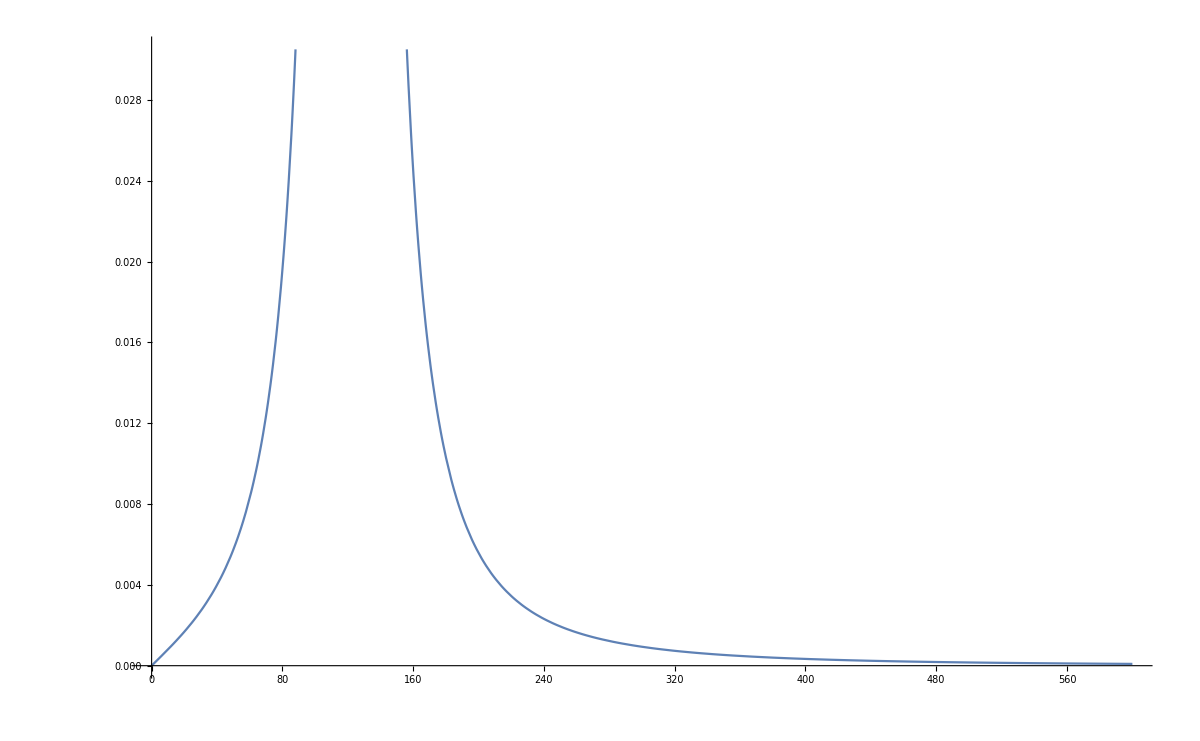

```mathematica
Plot[0.1239604148107294/((0.002652684134341411-(4 π^2)/λ^2)^2 λ^3),{λ,0,600},ImageSize->1200]
```

```mathematica
D[1+(4*π*n*q^2)/(m(Subscript[ω, 0]^2-(4π^2)/λ^2)),λ]
```

-(32 n π^3 q^2)/(m λ^3 (-(4 π^2)/λ^2+ω_0^2)^2)

```mathematica
FullSimplify[Sin[α]/(√(1-(Sin[Subscript[i, 1]]/n)^2)*√(1-n^2*(Sin[α]*√(1-(Sin[Subscript[i, 1]]/n)^2)+Cos[α]*Sin[Subscript[i, 1]]/n)^2))]
```

Sin[α]/(√(1-Sin[i_1]^2/n^2) √(1-(Cos[α] Sin[i_1]+n Sin[α] √(1-Sin[i_1]^2/n^2))^2))

```mathematica
α=π/10
```

π/10

```mathematica
n= 1.61
```

1.61

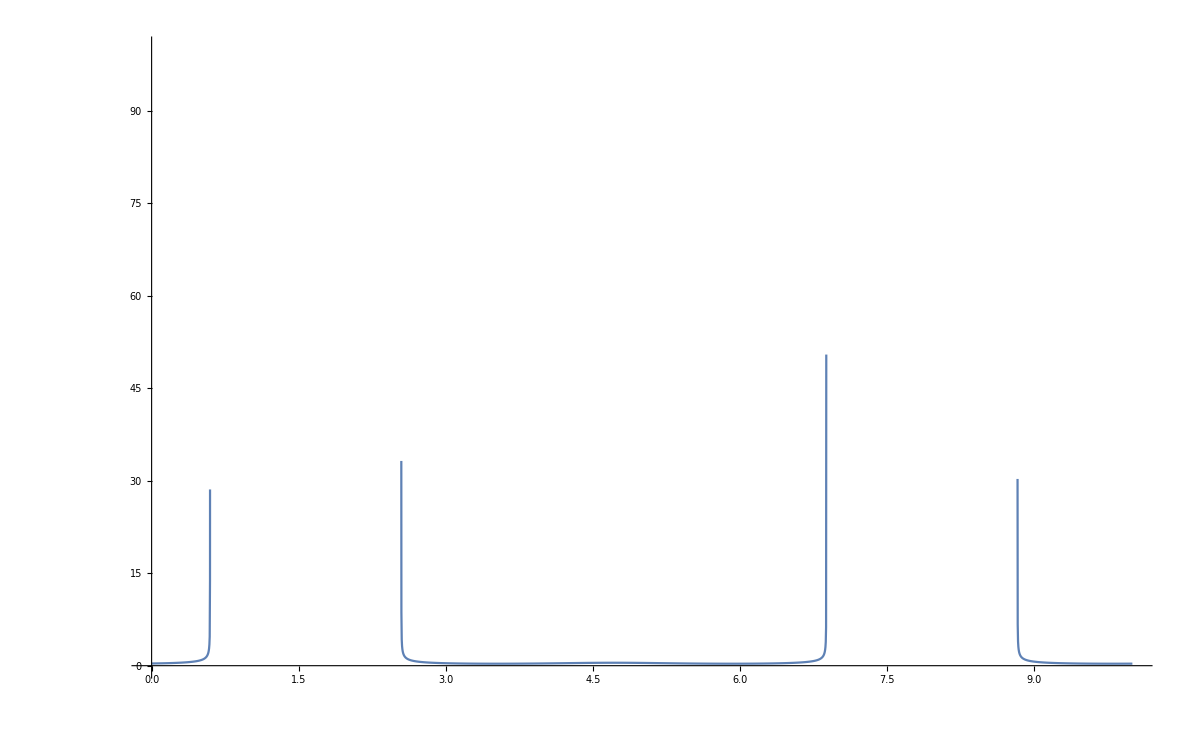

```mathematica
Plot[Sin[α]/(√(1-Sin[Subscript[i, 1]]^2/n^2) √(1-(Cos[α] Sin[Subscript[i, 1]]+n Sin[α] √(1-Sin[Subscript[i, 1]]^2/n^2))^2)),{Subscript[i, 1],0,10},ImageSize->1200,PlotRange->{{0,10},{0,100}}]
```

```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/3.5.3/353.xlsx,/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/3.5.3/~$353.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/3.5.3/353.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 1

```mathematica
dataset1=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"i","df"}/*Values]),{1,x},x]
```

FittedModel[-5920.05+91.7769 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5920.05 | 706.155 | -8.38349 | 0.00355948
x | 91.7769 | 9.36862 | 9.79621 | 0.00226069

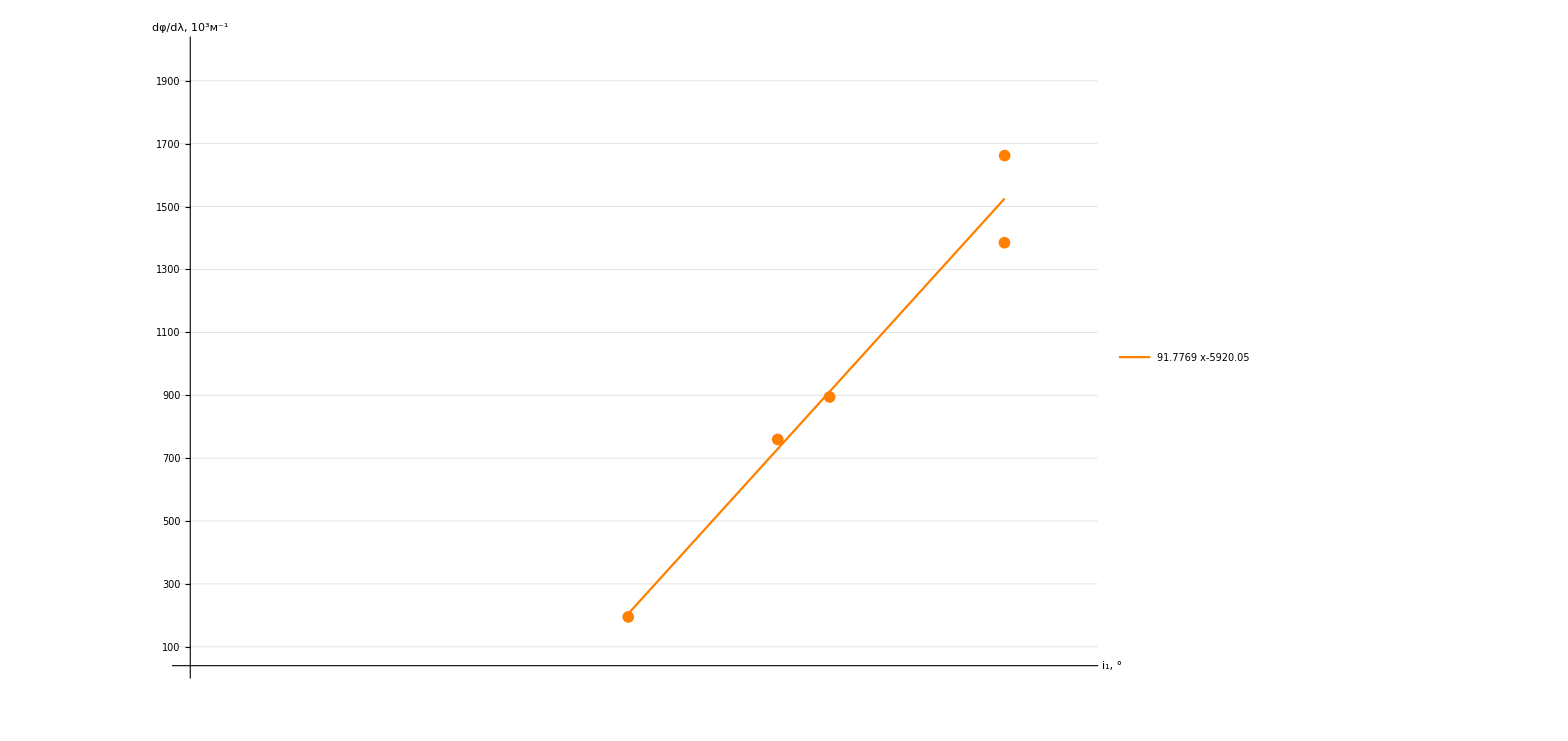

```mathematica
Show[
ListPlot[
dataset1,

PlotRange->{{50,84},{40,2000}},

Ticks-> {Range[-700,700,2],Range[-100,3000,100]},

GridLines->{Range[-1000,1000,0.5], Range[-1000,3000,50]},

AxesLabel->{Style["i_1, °",Large],Style["dφ/dλ, 10^3(:043c)^-1",Large]},

TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1200,
LabelStyle->Black,
PlotStyle->Orange
],
Plot[
{Normal@line1},
{x,66.7403, 81.1269},
PlotLegends->Placed[
LineLegend[ 
{Normal@line1, line1["ParameterTable"]},
LabelStyle->20,
LegendFunction->frame
],
{Scaled[0.21],Scaled[0.7]}
],
PlotStyle->Orange
]
]
```